```mathematica
Needs["FourierSeries`"]
```

```mathematica
Off[NIntegrate::inumr]
Off[NIntegrate::slwcon]
Off[NIntegrate::eincr]
Off[General::stop]
Off[NIntegrate::ncvb]
```

### Plot Options

```mathematica
SetOptions[Plot,PlotRange->All,Axes->False,PlotStyle->Thick,Frame->{True, True, False, False},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicksStyle->18,ImageSize->Medium];
SetOptions[LogPlot,PlotRange->All,Axes->False,PlotStyle->Thick,Frame->{True, True, False, False},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicksStyle->18,ImageSize->Medium];
SetOptions[LogLogPlot,PlotRange->All,Axes->False,PlotStyle->Thick,Frame->{True, True, False, False},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicksStyle->18,ImageSize->Medium];
SetOptions[LogLinearPlot,PlotRange->All,Axes->False,PlotStyle->Thick,Frame->{True, True, False, False},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicksStyle->18,ImageSize->Medium];
SetOptions[ListPlot,PlotRange->All,Axes->False,Joined->True,PlotStyle->Thick,Frame->{True, True, False, False},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicksStyle->18,ImageSize->Medium];
SetOptions[ListLogLinearPlot,PlotRange->All,Axes->False,PlotStyle->Thick,Frame->{True, True, False, False},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicksStyle->18,ImageSize->Medium];
SetOptions[ListLogPlot,PlotRange->All,Axes->False,PlotStyle->Thick,Frame->{True, True, False, False},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicksStyle->18,ImageSize->Medium];
SetOptions[ListLogLogPlot,PlotRange->All,Axes->False,PlotStyle->Thick,Frame->{True, True, False, False},FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicksStyle->18,ImageSize->Medium];
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}},GridLines->{{0},{0}},FrameLabel->(Style[#,22]&/@{"B_0(a)","dMC/dB_0 "})]]
```

```mathematica
TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},GridLines->{{0},{0}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}},FrameLabel->(Style[#,22]&/@{"B_0 (a)","MC"})]]
```

### Time dependence

Solve for time dependence of u and d in Fourier space:

```mathematica
dsol=Flatten[DSolve[{nu'[t]==-  k^2 nu[t]+ (b+β) I k nu[t]-0/2  nu[t]+0/2  nd[t],nd'[t]==-  k^2 nd[t]+ (-b+β) I k nd[t]-0/2  nd[t]+0/2  nu[t] ,nu[0]==δn/(2 π )^(1/2)Exp[-k^2 σ^2/2 ], nd[0]==-δn/(2 π )^(1/2)Exp[-k^2 σ^2/2 ]},{nu[t],nd[t]},t]]//FullSimplify;
```

```mathematica
{nd[t],nu[t]}/.{nu[t]->(ⅇ^(-1/2 k (-2 ⅈ t (b+ⅈ k+β)+k σ^2)) δn)/(√(2 π)),nd[t]->-(ⅇ^(-1/2 k (2 t (ⅈ b+k-ⅈ β)+k σ^2)) δn)/(√(2 π))}
```

{-(ⅇ^(-1/2 k (2 t (ⅈ b+k-ⅈ β)+k σ^2)) δn)/(√(2 π)),(ⅇ^(-1/2 k (-2 ⅈ t (b+ⅈ k+β)+k σ^2)) δn)/(√(2 π))}

```mathematica
u2 = nu[t]/.dsol
d2 = nd[t]/.dsol
```

(ⅇ^(-1/2 k (-2 ⅈ t (b+ⅈ k+β)+k σ^2)) δn)/(√(2 π))

-(ⅇ^(-1/2 k (2 t (ⅈ b+k-ⅈ β)+k σ^2)) δn)/(√(2 π))

```mathematica
{u[β_, b_,t_],d[β_, b_, t_]}={(ⅇ^(-1/2 t (1+√(1-4 b^2 k^2)+2 k (k-ⅈ β))-(k^2 σ^2)/2) (1-2 ⅈ b k+√(1-4 b^2 k^2)+ⅇ^(√(1-4 b^2 k^2) t) (-1+2 ⅈ b k+√(1-4 b^2 k^2))) δn)/(2 √(1-4 b^2 k^2) √(2 π)),-(ⅇ^(-1/2 t (1+√(1-4 b^2 k^2)+2 k (k-ⅈ β))-(k^2 σ^2)/2) (1+2 ⅈ b k+√(1-4 b^2 k^2)+ⅇ^(√(1-4 b^2 k^2) t) (-1-2 ⅈ b k+√(1-4 b^2 k^2))) δn)/(2 √(1-4 b^2 k^2) √(2 π))};
```

```mathematica
{u[β_, b_,t_],d[β_, b_, t_]}={(ⅇ^(-1/2 k (-2 ⅈ t (b+ⅈ k+β)+k σ^2)) δn)/(√(2 π)),-(ⅇ^(-1/2 k (2 t (ⅈ b+k-ⅈ β)+k σ^2)) δn)/(√(2 π))};
```

The following were long time approximations in dimensionful units. Not sure how they can be derived in the new units since D  = 0 was needed to be assumed.

Important modules that invert the Fourier Transform numerically:

```mathematica
ReferenceFrameModU[ β_,b_,time_]:=Module[{},

labz = ParallelTable[z,zRange];
movingz = ParallelTable[z+β time,zRange];

pts=ParallelTable[NInverseFourierTransform[u[β, b, time]/.params, k,z, FourierParameters->{0,-1}, MaxRecursion->12],zRange];
(*pts2=ParallelTable[NInverseFourierTransform[u[0, b,λ, time]/.params(*/.z->(z+β time)*), k,z, FourierParameters->{0,1}, MaxRecursion->12],zRange];*)

labU = Transpose[{labz, pts}]//Chop;
movingU = Transpose[{movingz, pts}]//Chop;

(*lab2U = Transpose[{labz, pts2}]//Chop;
moving2U = Transpose[{ParallelTable[z-β time,zRange], pts2}]//Chop;*)
(*moving2 = Transpose[{movingz, pts2}]//Chop;*)

Return[labU]

]
ReferenceFrameModD[ β_,b_,time_]:=Module[{},

labz = ParallelTable[z,zRange];
movingz = ParallelTable[z+β time,zRange];

pts=ParallelTable[NInverseFourierTransform[d[β, b, time]/.params, k,z, FourierParameters->{0,-1}, MaxRecursion->12],zRange];
(*pts2=ParallelTable[NInverseFourierTransform[d[0, b,λ, time]/.params(*/.z->(z+β time)*), k,z, FourierParameters->{0,1}, MaxRecursion->12],zRange];*)

labD = Transpose[{labz, pts}]//Chop;
movingD = Transpose[{movingz, pts}]//Chop;

(*lab2D = Transpose[{labz, pts2}]//Chop;
moving2D = Transpose[{ParallelTable[z-β time,zRange], pts2}]//Chop;*)
(*moving2 = Transpose[{movingz, pts2}]//Chop;*)

Return[labD]

]
```

```mathematica
params={ σ->0.01,δn->1};
zRange = {z,-30,30,0.3};
(* using units of ns and μm *)
(* b here is νb and assumes GaAs and b is 10^6 T/m*)
```

```mathematica
TIME = 10;
tabU=ReferenceFrameModU[0., 0,TIME];//AbsoluteTiming
```

{4.91003,Null}

```mathematica
TIME = 10;
tabD=ReferenceFrameModD[0., 0,TIME];//AbsoluteTiming
```

{6.18667,Null}

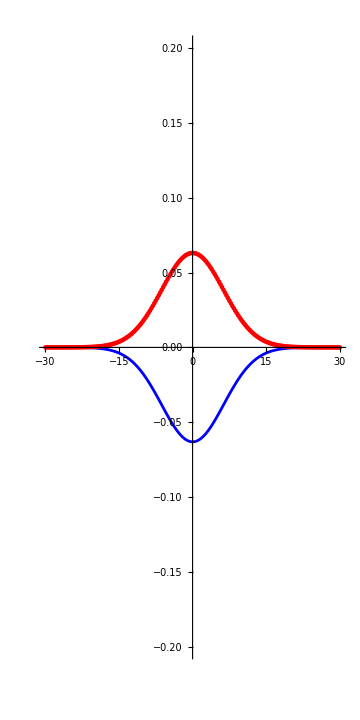

```mathematica
Eplot1=Show[ListPlot[tabU//Re, Joined->False, PlotRange->{{-30,30},{-0.2,0.2}}, PlotStyle->{{Red},{Red}, {Red},{Red}}, FrameLabel->(Style[#,22]&/@{"z","n_(↑,) n_↓"}), GridLines->{{0},{0}}, GridLinesStyle->{{Black,Thickness[0.005], Dashed},{}}],ListPlot[tabD//Re, Joined->True, PlotRange->{{-20,20},{-2,2}}, PlotStyle->{{Blue},{Blue}, {Blue},{Blue}}, FrameLabel->(Style[#,22]&/@{"z","n_(↑,) n_↓"}), GridLines->{-(1+0.5)*TIME,-(1+0.5)*2 TIME,-(1+0.5)*3 TIME,-(1+0.5)*4 TIME, (1-0.5)*TIME, (1-0.5)*2 TIME, (1-0.5)*3 TIME, (1-0.5)*4 TIME}, GridLinesStyle->Thickness[0.001]], AspectRatio->2]
```

### Big code

import numpy as np
x=np.sqrt(2)
particleList = [1,x,5,4,1]
particleList

{1,1.41421,5,4,1}

```mathematica
newList = %
```

{1,1.41421,5,4,1}

### code

import numpy as np
import math

def analyticSolution(x, t, v, D=1):    
    lead = 1 / math.sqrt(4 * math.pi * D * t)
    exponent = -1 * ((x - (v * t)) ** 2)/(4 * D * t)
    return lead * (math.e ** exponent)

# This is a function to generate a list of the solution values above
def makeSolutionList(increments, t, v, D=1):
    returnList = [] # List holds solutions
    xVal = -increments # Set the x-value to negative iterations, which is the farthest out a particle could get in these conditions
    while xVal <= increments: # Iterate through each value on the applicable x-axis 
        returnList.append(analyticSolution(xVal, t, v, D)) # Append the calculation with parameters
        xVal += 1
    return returnList


deltaT = 0.1
timeConst = 10
diffCon = 1
bSpin = 0
gamma = 0
numParticles = 10000

# Behavior of the simulation
# Number of iterations the simulation will move the particles through
# this is sent to int, so if the output is not a whole number it will go to the next smallest integer
increments = int (timeConst / deltaT)

particleRange = np.linspace(-increments, increments, increments*2 + 1)
solTopFreq = makeSolutionList(increments, timeConst, bSpin, diffCon)
solBottomFreq = makeSolutionList(increments, timeConst, -bSpin, diffCon)
solBottomFreq = [-item for item in solBottomFreq]
solTop = []
solBottom = []

for i in range(0, increments*2 + 1):
    solTop.append((particleRange[i], solTopFreq[i]))
    solBottom.append((particleRange[i], solBottomFreq[i]))

totalData = [solTop, solBottom]
totalData

{{{-200.,4.49406×10^-219},{-199.,6.58693×10^-217},{-198.,9.41606×10^-215},{-197.,1.3128×10^-212},{-196.,1.78513×10^-210},{-195.,2.36747×10^-208},{-194.,3.06225×10^-206},{-193.,3.86314×10^-204},{-192.,4.75316×10^-202},{-191.,5.70384×10^-200},{-190.,6.67567×10^-198},{-189.,7.62018×10^-196},{-188.,8.48356×10^-194},{-187.,9.21156×10^-192},{-186.,9.75509×10^-190},{-185.,1.00756×10^-187},{-184.,1.01497×10^-185},{-183.,9.97198×10^-184},{-182.,9.55542×10^-182},{-181.,8.9302×10^-180},{-180.,8.13982×10^-178},{-179.,7.23621×10^-176},{-178.,6.27409×10^-174},{-177.,5.30557×10^-172},{-176.,4.37579×10^-170},{-175.,3.51985×10^-168},{-174.,2.76143×10^-166},{-173.,2.11293×10^-164},{-172.,1.57681×10^-162},{-171.,1.14767×10^-160},{-170.,8.14701×10^-159},{-169.,5.64055×10^-157},{-168.,3.80879×10^-155},{-167.,2.50839×10^-153},{-166.,1.61119×10^-151},{-165.,1.00934×10^-149},{-164.,6.16702×10^-148},{-163.,3.67497×10^-146},{-162.,2.13587×10^-144},{-161.,1.21071×10^-142},{-160.,6.69339×10^-141},{-159.,3.60907×10^-139},{-158.,1.89796×10^-137},{-157.,9.73468×10^-136},{-156.,4.86966×10^-134},{-155.,2.37585×10^-132},{-154.,1.13053×10^-130},{-153.,5.2467×10^-129},{-152.,2.37484×10^-127},{-151.,1.04839×10^-125},{-150.,4.51395×10^-124},{-149.,1.89554×10^-122},{-148.,7.76338×10^-121},{-147.,3.10107×10^-119},{-146.,1.20813×10^-117},{-145.,4.59052×10^-116},{-144.,1.70118×10^-114},{-143.,6.14868×10^-113},{-142.,2.16748×10^-111},{-141.,7.452×10^-110},{-140.,2.4988×10^-108},{-139.,8.17211×10^-107},{-138.,2.60663×10^-105},{-137.,8.10897×10^-104},{-136.,2.46034×10^-102},{-135.,7.28062×10^-101},{-134.,2.10128×10^-99},{-133.,5.91482×10^-98},{-132.,1.62384×10^-96},{-131.,4.34795×10^-95},{-130.,1.13546×10^-93},{-129.,2.89201×10^-92},{-128.,7.18406×10^-91},{-127.,1.74054×10^-89},{-126.,4.11282×10^-88},{-125.,9.47849×10^-87},{-124.,2.1305×10^-85},{-123.,4.67052×10^-84},{-122.,9.986×10^-83},{-121.,2.08239×10^-81},{-120.,4.23519×10^-80},{-119.,8.40094×10^-79},{-118.,1.62527×10^-77},{-117.,3.06666×10^-76},{-116.,5.6435×10^-75},{-115.,1.01292×10^-73},{-114.,1.77313×10^-72},{-113.,3.02728×10^-71},{-112.,5.04087×10^-70},{-111.,8.18655×10^-69},{-110.,1.2967×10^-67},{-109.,2.00318×10^-66},{-108.,3.01818×10^-65},{-107.,4.43518×10^-64},{-106.,6.35653×10^-63},{-105.,8.88529×10^-62},{-104.,1.21134×10^-60},{-103.,1.61066×10^-59},{-102.,2.08873×10^-58},{-101.,2.64183×10^-57},{-100.,3.25889×10^-56},{-99.,3.92082×10^-55},{-98.,4.60074×10^-54},{-97.,5.26527×10^-53},{-96.,5.877×10^-52},{-95.,6.39785×10^-51},{-94.,6.79289×10^-50},{-93.,7.03425×10^-49},{-92.,7.10434×10^-48},{-91.,6.99798×10^-47},{-90.,6.72301×10^-46},{-89.,6.29938×10^-45},{-88.,5.75671×10^-44},{-87.,5.1309×10^-43},{-86.,4.46021×10^-42},{-85.,3.78146×10^-41},{-84.,3.12685×10^-40},{-83.,2.52172×10^-39},{-82.,1.98348×10^-38},{-81.,1.52161×10^-37},{-80.,1.13847×10^-36},{-79.,8.30772×10^-36},{-78.,5.91268×10^-35},{-77.,4.10422×10^-34},{-76.,2.77855×10^-33},{-75.,1.83463×10^-32},{-74.,1.18147×10^-31},{-73.,7.4206×10^-31},{-72.,4.54567×10^-30},{-71.,2.71581×10^-29},{-70.,1.5825×10^-28},{-69.,8.99352×10^-28},{-68.,4.98493×10^-27},{-67.,2.69483×10^-26},{-66.,1.42084×10^-25},{-65.,7.30639×10^-25},{-64.,3.6644×10^-24},{-63.,1.79244×10^-23},{-62.,8.55126×10^-23},{-61.,3.97885×10^-22},{-60.,1.80563×10^-21},{-59.,7.99174×10^-21},{-58.,3.44983×10^-20},{-57.,1.45243×10^-19},{-56.,5.96398×10^-19},{-55.,2.38847×10^-18},{-54.,9.32924×10^-18},{-53.,3.55398×10^-17},{-52.,1.32046×10^-16},{-51.,4.78499×10^-16},{-50.,1.69113×10^-15},{-49.,5.82931×10^-15},{-48.,1.95974×10^-14},{-47.,6.42575×10^-14},{-46.,2.0549×10^-13},{-45.,6.40916×10^-13},{-44.,1.94964×10^-12},{-43.,5.78427×10^-12},{-42.,1.67374×10^-11},{-41.,4.72354×10^-11},{-40.,1.30014×10^-10},{-39.,3.49025×10^-10},{-38.,9.13828×10^-10},{-37.,2.33354×10^-9},{-36.,5.81178×10^-9},{-35.,1.41171×10^-8},{-34.,3.34445×10^-8},{-33.,7.72763×10^-8},{-32.,1.74145×10^-7},{-31.,3.82752×10^-7},{-30.,8.20478×10^-7},{-29.,1.71538×10^-6},{-28.,3.49779×10^-6},{-27.,6.95619×10^-6},{-26.,0.0000134925},{-25.,0.0000255243},{-24.,0.0000470934},{-23.,0.0000847438},{-22.,0.00014873},{-21.,0.000254584},{-20.,0.000425018},{-19.,0.000692032},{-18.,0.00109897},{-17.,0.00170212},{-16.,0.00257121},{-15.,0.00378815},{-14.,0.00544325},{-13.,0.00762839},{-12.,0.0104268},{-11.,0.0138998},{-10.,0.0180722},{-9.,0.022917},{-8.,0.0283429},{-7.,0.0341881},{-6.,0.0402205},{-5.,0.0461491},{-4.,0.0516442},{-3.,0.0563666},{-2.,0.0600019},{-1.,0.0622947},{0.,0.0630783},{1.,0.0622947},{2.,0.0600019},{3.,0.0563666},{4.,0.0516442},{5.,0.0461491},{6.,0.0402205},{7.,0.0341881},{8.,0.0283429},{9.,0.022917},{10.,0.0180722},{11.,0.0138998},{12.,0.0104268},{13.,0.00762839},{14.,0.00544325},{15.,0.00378815},{16.,0.00257121},{17.,0.00170212},{18.,0.00109897},{19.,0.000692032},{20.,0.000425018},{21.,0.000254584},{22.,0.00014873},{23.,0.0000847438},{24.,0.0000470934},{25.,0.0000255243},{26.,0.0000134925},{27.,6.95619×10^-6},{28.,3.49779×10^-6},{29.,1.71538×10^-6},{30.,8.20478×10^-7},{31.,3.82752×10^-7},{32.,1.74145×10^-7},{33.,7.72763×10^-8},{34.,3.34445×10^-8},{35.,1.41171×10^-8},{36.,5.81178×10^-9},{37.,2.33354×10^-9},{38.,9.13828×10^-10},{39.,3.49025×10^-10},{40.,1.30014×10^-10},{41.,4.72354×10^-11},{42.,1.67374×10^-11},{43.,5.78427×10^-12},{44.,1.94964×10^-12},{45.,6.40916×10^-13},{46.,2.0549×10^-13},{47.,6.42575×10^-14},{48.,1.95974×10^-14},{49.,5.82931×10^-15},{50.,1.69113×10^-15},{51.,4.78499×10^-16},{52.,1.32046×10^-16},{53.,3.55398×10^-17},{54.,9.32924×10^-18},{55.,2.38847×10^-18},{56.,5.96398×10^-19},{57.,1.45243×10^-19},{58.,3.44983×10^-20},{59.,7.99174×10^-21},{60.,1.80563×10^-21},{61.,3.97885×10^-22},{62.,8.55126×10^-23},{63.,1.79244×10^-23},{64.,3.6644×10^-24},{65.,7.30639×10^-25},{66.,1.42084×10^-25},{67.,2.69483×10^-26},{68.,4.98493×10^-27},{69.,8.99352×10^-28},{70.,1.5825×10^-28},{71.,2.71581×10^-29},{72.,4.54567×10^-30},{73.,7.4206×10^-31},{74.,1.18147×10^-31},{75.,1.83463×10^-32},{76.,2.77855×10^-33},{77.,4.10422×10^-34},{78.,5.91268×10^-35},{79.,8.30772×10^-36},{80.,1.13847×10^-36},{81.,1.52161×10^-37},{82.,1.98348×10^-38},{83.,2.52172×10^-39},{84.,3.12685×10^-40},{85.,3.78146×10^-41},{86.,4.46021×10^-42},{87.,5.1309×10^-43},{88.,5.75671×10^-44},{89.,6.29938×10^-45},{90.,6.72301×10^-46},{91.,6.99798×10^-47},{92.,7.10434×10^-48},{93.,7.03425×10^-49},{94.,6.79289×10^-50},{95.,6.39785×10^-51},{96.,5.877×10^-52},{97.,5.26527×10^-53},{98.,4.60074×10^-54},{99.,3.92082×10^-55},{100.,3.25889×10^-56},{101.,2.64183×10^-57},{102.,2.08873×10^-58},{103.,1.61066×10^-59},{104.,1.21134×10^-60},{105.,8.88529×10^-62},{106.,6.35653×10^-63},{107.,4.43518×10^-64},{108.,3.01818×10^-65},{109.,2.00318×10^-66},{110.,1.2967×10^-67},{111.,8.18655×10^-69},{112.,5.04087×10^-70},{113.,3.02728×10^-71},{114.,1.77313×10^-72},{115.,1.01292×10^-73},{116.,5.6435×10^-75},{117.,3.06666×10^-76},{118.,1.62527×10^-77},{119.,8.40094×10^-79},{120.,4.23519×10^-80},{121.,2.08239×10^-81},{122.,9.986×10^-83},{123.,4.67052×10^-84},{124.,2.1305×10^-85},{125.,9.47849×10^-87},{126.,4.11282×10^-88},{127.,1.74054×10^-89},{128.,7.18406×10^-91},{129.,2.89201×10^-92},{130.,1.13546×10^-93},{131.,4.34795×10^-95},{132.,1.62384×10^-96},{133.,5.91482×10^-98},{134.,2.10128×10^-99},{135.,7.28062×10^-101},{136.,2.46034×10^-102},{137.,8.10897×10^-104},{138.,2.60663×10^-105},{139.,8.17211×10^-107},{140.,2.4988×10^-108},{141.,7.452×10^-110},{142.,2.16748×10^-111},{143.,6.14868×10^-113},{144.,1.70118×10^-114},{145.,4.59052×10^-116},{146.,1.20813×10^-117},{147.,3.10107×10^-119},{148.,7.76338×10^-121},{149.,1.89554×10^-122},{150.,4.51395×10^-124},{151.,1.04839×10^-125},{152.,2.37484×10^-127},{153.,5.2467×10^-129},{154.,1.13053×10^-130},{155.,2.37585×10^-132},{156.,4.86966×10^-134},{157.,9.73468×10^-136},{158.,1.89796×10^-137},{159.,3.60907×10^-139},{160.,6.69339×10^-141},{161.,1.21071×10^-142},{162.,2.13587×10^-144},{163.,3.67497×10^-146},{164.,6.16702×10^-148},{165.,1.00934×10^-149},{166.,1.61119×10^-151},{167.,2.50839×10^-153},{168.,3.80879×10^-155},{169.,5.64055×10^-157},{170.,8.14701×10^-159},{171.,1.14767×10^-160},{172.,1.57681×10^-162},{173.,2.11293×10^-164},{174.,2.76143×10^-166},{175.,3.51985×10^-168},{176.,4.37579×10^-170},{177.,5.30557×10^-172},{178.,6.27409×10^-174},{179.,7.23621×10^-176},{180.,8.13982×10^-178},{181.,8.9302×10^-180},{182.,9.55542×10^-182},{183.,9.97198×10^-184},{184.,1.01497×10^-185},{185.,1.00756×10^-187},{186.,9.75509×10^-190},{187.,9.21156×10^-192},{188.,8.48356×10^-194},{189.,7.62018×10^-196},{190.,6.67567×10^-198},{191.,5.70384×10^-200},{192.,4.75316×10^-202},{193.,3.86314×10^-204},{194.,3.06225×10^-206},{195.,2.36747×10^-208},{196.,1.78513×10^-210},{197.,1.3128×10^-212},{198.,9.41606×10^-215},{199.,6.58693×10^-217},{200.,4.49406×10^-219}},{{-200.,-4.49406×10^-219},{-199.,-6.58693×10^-217},{-198.,-9.41606×10^-215},{-197.,-1.3128×10^-212},{-196.,-1.78513×10^-210},{-195.,-2.36747×10^-208},{-194.,-3.06225×10^-206},{-193.,-3.86314×10^-204},{-192.,-4.75316×10^-202},{-191.,-5.70384×10^-200},{-190.,-6.67567×10^-198},{-189.,-7.62018×10^-196},{-188.,-8.48356×10^-194},{-187.,-9.21156×10^-192},{-186.,-9.75509×10^-190},{-185.,-1.00756×10^-187},{-184.,-1.01497×10^-185},{-183.,-9.97198×10^-184},{-182.,-9.55542×10^-182},{-181.,-8.9302×10^-180},{-180.,-8.13982×10^-178},{-179.,-7.23621×10^-176},{-178.,-6.27409×10^-174},{-177.,-5.30557×10^-172},{-176.,-4.37579×10^-170},{-175.,-3.51985×10^-168},{-174.,-2.76143×10^-166},{-173.,-2.11293×10^-164},{-172.,-1.57681×10^-162},{-171.,-1.14767×10^-160},{-170.,-8.14701×10^-159},{-169.,-5.64055×10^-157},{-168.,-3.80879×10^-155},{-167.,-2.50839×10^-153},{-166.,-1.61119×10^-151},{-165.,-1.00934×10^-149},{-164.,-6.16702×10^-148},{-163.,-3.67497×10^-146},{-162.,-2.13587×10^-144},{-161.,-1.21071×10^-142},{-160.,-6.69339×10^-141},{-159.,-3.60907×10^-139},{-158.,-1.89796×10^-137},{-157.,-9.73468×10^-136},{-156.,-4.86966×10^-134},{-155.,-2.37585×10^-132},{-154.,-1.13053×10^-130},{-153.,-5.2467×10^-129},{-152.,-2.37484×10^-127},{-151.,-1.04839×10^-125},{-150.,-4.51395×10^-124},{-149.,-1.89554×10^-122},{-148.,-7.76338×10^-121},{-147.,-3.10107×10^-119},{-146.,-1.20813×10^-117},{-145.,-4.59052×10^-116},{-144.,-1.70118×10^-114},{-143.,-6.14868×10^-113},{-142.,-2.16748×10^-111},{-141.,-7.452×10^-110},{-140.,-2.4988×10^-108},{-139.,-8.17211×10^-107},{-138.,-2.60663×10^-105},{-137.,-8.10897×10^-104},{-136.,-2.46034×10^-102},{-135.,-7.28062×10^-101},{-134.,-2.10128×10^-99},{-133.,-5.91482×10^-98},{-132.,-1.62384×10^-96},{-131.,-4.34795×10^-95},{-130.,-1.13546×10^-93},{-129.,-2.89201×10^-92},{-128.,-7.18406×10^-91},{-127.,-1.74054×10^-89},{-126.,-4.11282×10^-88},{-125.,-9.47849×10^-87},{-124.,-2.1305×10^-85},{-123.,-4.67052×10^-84},{-122.,-9.986×10^-83},{-121.,-2.08239×10^-81},{-120.,-4.23519×10^-80},{-119.,-8.40094×10^-79},{-118.,-1.62527×10^-77},{-117.,-3.06666×10^-76},{-116.,-5.6435×10^-75},{-115.,-1.01292×10^-73},{-114.,-1.77313×10^-72},{-113.,-3.02728×10^-71},{-112.,-5.04087×10^-70},{-111.,-8.18655×10^-69},{-110.,-1.2967×10^-67},{-109.,-2.00318×10^-66},{-108.,-3.01818×10^-65},{-107.,-4.43518×10^-64},{-106.,-6.35653×10^-63},{-105.,-8.88529×10^-62},{-104.,-1.21134×10^-60},{-103.,-1.61066×10^-59},{-102.,-2.08873×10^-58},{-101.,-2.64183×10^-57},{-100.,-3.25889×10^-56},{-99.,-3.92082×10^-55},{-98.,-4.60074×10^-54},{-97.,-5.26527×10^-53},{-96.,-5.877×10^-52},{-95.,-6.39785×10^-51},{-94.,-6.79289×10^-50},{-93.,-7.03425×10^-49},{-92.,-7.10434×10^-48},{-91.,-6.99798×10^-47},{-90.,-6.72301×10^-46},{-89.,-6.29938×10^-45},{-88.,-5.75671×10^-44},{-87.,-5.1309×10^-43},{-86.,-4.46021×10^-42},{-85.,-3.78146×10^-41},{-84.,-3.12685×10^-40},{-83.,-2.52172×10^-39},{-82.,-1.98348×10^-38},{-81.,-1.52161×10^-37},{-80.,-1.13847×10^-36},{-79.,-8.30772×10^-36},{-78.,-5.91268×10^-35},{-77.,-4.10422×10^-34},{-76.,-2.77855×10^-33},{-75.,-1.83463×10^-32},{-74.,-1.18147×10^-31},{-73.,-7.4206×10^-31},{-72.,-4.54567×10^-30},{-71.,-2.71581×10^-29},{-70.,-1.5825×10^-28},{-69.,-8.99352×10^-28},{-68.,-4.98493×10^-27},{-67.,-2.69483×10^-26},{-66.,-1.42084×10^-25},{-65.,-7.30639×10^-25},{-64.,-3.6644×10^-24},{-63.,-1.79244×10^-23},{-62.,-8.55126×10^-23},{-61.,-3.97885×10^-22},{-60.,-1.80563×10^-21},{-59.,-7.99174×10^-21},{-58.,-3.44983×10^-20},{-57.,-1.45243×10^-19},{-56.,-5.96398×10^-19},{-55.,-2.38847×10^-18},{-54.,-9.32924×10^-18},{-53.,-3.55398×10^-17},{-52.,-1.32046×10^-16},{-51.,-4.78499×10^-16},{-50.,-1.69113×10^-15},{-49.,-5.82931×10^-15},{-48.,-1.95974×10^-14},{-47.,-6.42575×10^-14},{-46.,-2.0549×10^-13},{-45.,-6.40916×10^-13},{-44.,-1.94964×10^-12},{-43.,-5.78427×10^-12},{-42.,-1.67374×10^-11},{-41.,-4.72354×10^-11},{-40.,-1.30014×10^-10},{-39.,-3.49025×10^-10},{-38.,-9.13828×10^-10},{-37.,-2.33354×10^-9},{-36.,-5.81178×10^-9},{-35.,-1.41171×10^-8},{-34.,-3.34445×10^-8},{-33.,-7.72763×10^-8},{-32.,-1.74145×10^-7},{-31.,-3.82752×10^-7},{-30.,-8.20478×10^-7},{-29.,-1.71538×10^-6},{-28.,-3.49779×10^-6},{-27.,-6.95619×10^-6},{-26.,-0.0000134925},{-25.,-0.0000255243},{-24.,-0.0000470934},{-23.,-0.0000847438},{-22.,-0.00014873},{-21.,-0.000254584},{-20.,-0.000425018},{-19.,-0.000692032},{-18.,-0.00109897},{-17.,-0.00170212},{-16.,-0.00257121},{-15.,-0.00378815},{-14.,-0.00544325},{-13.,-0.00762839},{-12.,-0.0104268},{-11.,-0.0138998},{-10.,-0.0180722},{-9.,-0.022917},{-8.,-0.0283429},{-7.,-0.0341881},{-6.,-0.0402205},{-5.,-0.0461491},{-4.,-0.0516442},{-3.,-0.0563666},{-2.,-0.0600019},{-1.,-0.0622947},{0.,-0.0630783},{1.,-0.0622947},{2.,-0.0600019},{3.,-0.0563666},{4.,-0.0516442},{5.,-0.0461491},{6.,-0.0402205},{7.,-0.0341881},{8.,-0.0283429},{9.,-0.022917},{10.,-0.0180722},{11.,-0.0138998},{12.,-0.0104268},{13.,-0.00762839},{14.,-0.00544325},{15.,-0.00378815},{16.,-0.00257121},{17.,-0.00170212},{18.,-0.00109897},{19.,-0.000692032},{20.,-0.000425018},{21.,-0.000254584},{22.,-0.00014873},{23.,-0.0000847438},{24.,-0.0000470934},{25.,-0.0000255243},{26.,-0.0000134925},{27.,-6.95619×10^-6},{28.,-3.49779×10^-6},{29.,-1.71538×10^-6},{30.,-8.20478×10^-7},{31.,-3.82752×10^-7},{32.,-1.74145×10^-7},{33.,-7.72763×10^-8},{34.,-3.34445×10^-8},{35.,-1.41171×10^-8},{36.,-5.81178×10^-9},{37.,-2.33354×10^-9},{38.,-9.13828×10^-10},{39.,-3.49025×10^-10},{40.,-1.30014×10^-10},{41.,-4.72354×10^-11},{42.,-1.67374×10^-11},{43.,-5.78427×10^-12},{44.,-1.94964×10^-12},{45.,-6.40916×10^-13},{46.,-2.0549×10^-13},{47.,-6.42575×10^-14},{48.,-1.95974×10^-14},{49.,-5.82931×10^-15},{50.,-1.69113×10^-15},{51.,-4.78499×10^-16},{52.,-1.32046×10^-16},{53.,-3.55398×10^-17},{54.,-9.32924×10^-18},{55.,-2.38847×10^-18},{56.,-5.96398×10^-19},{57.,-1.45243×10^-19},{58.,-3.44983×10^-20},{59.,-7.99174×10^-21},{60.,-1.80563×10^-21},{61.,-3.97885×10^-22},{62.,-8.55126×10^-23},{63.,-1.79244×10^-23},{64.,-3.6644×10^-24},{65.,-7.30639×10^-25},{66.,-1.42084×10^-25},{67.,-2.69483×10^-26},{68.,-4.98493×10^-27},{69.,-8.99352×10^-28},{70.,-1.5825×10^-28},{71.,-2.71581×10^-29},{72.,-4.54567×10^-30},{73.,-7.4206×10^-31},{74.,-1.18147×10^-31},{75.,-1.83463×10^-32},{76.,-2.77855×10^-33},{77.,-4.10422×10^-34},{78.,-5.91268×10^-35},{79.,-8.30772×10^-36},{80.,-1.13847×10^-36},{81.,-1.52161×10^-37},{82.,-1.98348×10^-38},{83.,-2.52172×10^-39},{84.,-3.12685×10^-40},{85.,-3.78146×10^-41},{86.,-4.46021×10^-42},{87.,-5.1309×10^-43},{88.,-5.75671×10^-44},{89.,-6.29938×10^-45},{90.,-6.72301×10^-46},{91.,-6.99798×10^-47},{92.,-7.10434×10^-48},{93.,-7.03425×10^-49},{94.,-6.79289×10^-50},{95.,-6.39785×10^-51},{96.,-5.877×10^-52},{97.,-5.26527×10^-53},{98.,-4.60074×10^-54},{99.,-3.92082×10^-55},{100.,-3.25889×10^-56},{101.,-2.64183×10^-57},{102.,-2.08873×10^-58},{103.,-1.61066×10^-59},{104.,-1.21134×10^-60},{105.,-8.88529×10^-62},{106.,-6.35653×10^-63},{107.,-4.43518×10^-64},{108.,-3.01818×10^-65},{109.,-2.00318×10^-66},{110.,-1.2967×10^-67},{111.,-8.18655×10^-69},{112.,-5.04087×10^-70},{113.,-3.02728×10^-71},{114.,-1.77313×10^-72},{115.,-1.01292×10^-73},{116.,-5.6435×10^-75},{117.,-3.06666×10^-76},{118.,-1.62527×10^-77},{119.,-8.40094×10^-79},{120.,-4.23519×10^-80},{121.,-2.08239×10^-81},{122.,-9.986×10^-83},{123.,-4.67052×10^-84},{124.,-2.1305×10^-85},{125.,-9.47849×10^-87},{126.,-4.11282×10^-88},{127.,-1.74054×10^-89},{128.,-7.18406×10^-91},{129.,-2.89201×10^-92},{130.,-1.13546×10^-93},{131.,-4.34795×10^-95},{132.,-1.62384×10^-96},{133.,-5.91482×10^-98},{134.,-2.10128×10^-99},{135.,-7.28062×10^-101},{136.,-2.46034×10^-102},{137.,-8.10897×10^-104},{138.,-2.60663×10^-105},{139.,-8.17211×10^-107},{140.,-2.4988×10^-108},{141.,-7.452×10^-110},{142.,-2.16748×10^-111},{143.,-6.14868×10^-113},{144.,-1.70118×10^-114},{145.,-4.59052×10^-116},{146.,-1.20813×10^-117},{147.,-3.10107×10^-119},{148.,-7.76338×10^-121},{149.,-1.89554×10^-122},{150.,-4.51395×10^-124},{151.,-1.04839×10^-125},{152.,-2.37484×10^-127},{153.,-5.2467×10^-129},{154.,-1.13053×10^-130},{155.,-2.37585×10^-132},{156.,-4.86966×10^-134},{157.,-9.73468×10^-136},{158.,-1.89796×10^-137},{159.,-3.60907×10^-139},{160.,-6.69339×10^-141},{161.,-1.21071×10^-142},{162.,-2.13587×10^-144},{163.,-3.67497×10^-146},{164.,-6.16702×10^-148},{165.,-1.00934×10^-149},{166.,-1.61119×10^-151},{167.,-2.50839×10^-153},{168.,-3.80879×10^-155},{169.,-5.64055×10^-157},{170.,-8.14701×10^-159},{171.,-1.14767×10^-160},{172.,-1.57681×10^-162},{173.,-2.11293×10^-164},{174.,-2.76143×10^-166},{175.,-3.51985×10^-168},{176.,-4.37579×10^-170},{177.,-5.30557×10^-172},{178.,-6.27409×10^-174},{179.,-7.23621×10^-176},{180.,-8.13982×10^-178},{181.,-8.9302×10^-180},{182.,-9.55542×10^-182},{183.,-9.97198×10^-184},{184.,-1.01497×10^-185},{185.,-1.00756×10^-187},{186.,-9.75509×10^-190},{187.,-9.21156×10^-192},{188.,-8.48356×10^-194},{189.,-7.62018×10^-196},{190.,-6.67567×10^-198},{191.,-5.70384×10^-200},{192.,-4.75316×10^-202},{193.,-3.86314×10^-204},{194.,-3.06225×10^-206},{195.,-2.36747×10^-208},{196.,-1.78513×10^-210},{197.,-1.3128×10^-212},{198.,-9.41606×10^-215},{199.,-6.58693×10^-217},{200.,-4.49406×10^-219}}}

```mathematica
dataFromPython = %;
```

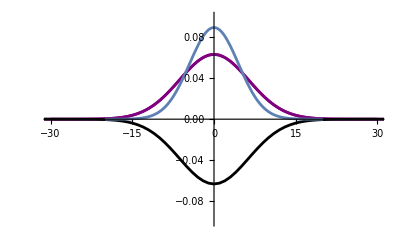

```mathematica
(*particlesTop = dataFromPython[[1]];
particlesBottom = dataFromPython[[2]];*)
solTop = dataFromPython[[1]];
solBottom = dataFromPython[[2]];
(*listLength = Length[particlesBottom];
up = particlesTop⟦1;;listLength;;2⟧;
down = particlesBottom⟦1;;listLength;;2⟧;*)
analyticSolution = (1/Sqrt[4Pi*t])*Exp[-(x-v*t)^2/(4*t)];


Show[
ListPlot[MapApply[{#1, 1#2}&]@tabU//Re, Joined->True, PlotRange->{{-30,30},{-0.1,0.1}},  PlotStyle->{{Purple},{Purple}, {Purple},{Purple}} , GridLines->{{0},{0}}], 
(*ListPlot[MapApply[{#1, √(8 0.1)#2}&]@tabD//Re, Joined->True, PlotRange->{{-30,30},{-0.1,0.1}},PlotStyle->{{Blue},{Blue}, {Blue},{Blue}}], *)
(*MapApply[{#1, √(8 0.1)#2}&]@*)
ListPlot[solTop, Joined->True, PlotRange->{{-20,20},{-0.1,0.1}},PlotStyle->{{Purple},{Purple}, {Purple},{Purple}}],
ListPlot[solBottom, Joined->True, PlotRange->{{-20,20},{-0.1,0.1}},  PlotStyle->{{Black},{Black}, {Black},{Black}} ], 
(*ListPlot[up, Joined->False, PlotRange->{{-30,30},{-0.1,0.1}},PlotStyle->{{Orange},{Orange}, {Orange},{Orange}} ],
ListPlot[down, Joined->False, PlotRange->{{-30,30},{-0.1,0.1}},  PlotStyle->{{Brown},{Brown}, {Brown},{Brown}} ],*) Plot[1.analyticSolution/.{v->0,t->10},{x,-20,20}]]
```

scaling factor does not depend on b nor time.

Could sqrt 8 actully be sqrt(2 π)?

```mathematica
√8.
```

2.82843

```mathematica
√(2. π)
```

2.50663

Seems too far off.

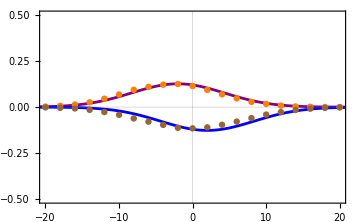

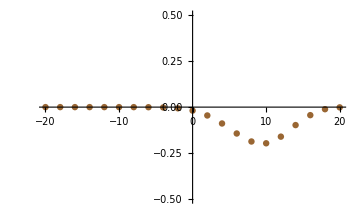

```mathematica
ListPlot[down, Joined->False
, PlotRange->{{-20,20},{-0.5,0.5}},  PlotStyle->{{Brown},{Brown}, {Brown},{Brown}} ]
```

```mathematica
Part[MapApply[{#1,2 #2}&]@tabU,10]
```

{-19.1,0}

```mathematica
tabU
```

{{-20.,0},{-19.9,0},{-19.8,0},{-19.7,0},{-19.6,0},{-19.5,0},{-19.4,0},{-19.3,0},{-19.2,0},{-19.1,0},{-19.,0},{-18.9,0},{-18.8,0},{-18.7,0},{-18.6,0},{-18.5,0},{-18.4,0},{-18.3,0},{-18.2,0},{-18.1,0},{-18.,0},{-17.9,0},{-17.8,0},{-17.7,0},{-17.6,0},{-17.5,0},{-17.4,0},{-17.3,0},{-17.2,0},{-17.1,0},{-17.,0},{-16.9,0},{-16.8,0},{-16.7,0},{-16.6,0},{-16.5,0},{-16.4,0},{-16.3,0},{-16.2,0},{-16.1,0},{-16.,0},{-15.9,0},{-15.8,0},{-15.7,0},{-15.6,0},{-15.5,0},{-15.4,0},{-15.3,0},{-15.2,0},{-15.1,0},{-15.,0},{-14.9,0},{-14.8,0},{-14.7,0},{-14.6,0},{-14.5,0},{-14.4,0},{-14.3,0},{-14.2,0},{-14.1,0},{-14.,0},{-13.9,0},{-13.8,0},{-13.7,0},{-13.6,0},{-13.5,0},{-13.4,0},{-13.3,0},{-13.2,0},{-13.1,0},{-13.,0},{-12.9,0},{-12.8,0},{-12.7,0},{-12.6,0},{-12.5,0},{-12.4,0},{-12.3,0},{-12.2,0},{-12.1,0},{-12.,0},{-11.9,0},{-11.8,0},{-11.7,0},{-11.6,0},{-11.5,0},{-11.4,0},{-11.3,0},{-11.2,0},{-11.1,0},{-11.,0},{-10.9,0},{-10.8,0},{-10.7,0},{-10.6,0},{-10.5,0},{-10.4,0},{-10.3,0},{-10.2,0},{-10.1,0},{-10.,0},{-9.9,0},{-9.8,0},{-9.7,0},{-9.6,0},{-9.5,0},{-9.4,0},{-9.3,1.149×10^-10},{-9.2,1.82462×10^-10},{-9.1,2.88305×10^-10},{-9.,4.53274×10^-10},{-8.9,7.09084×10^-10},{-8.8,1.10373×10^-9},{-8.7,1.70946×10^-9},{-8.6,2.63439×10^-9},{-8.5,4.03954×10^-9},{-8.4,6.16329×10^-9},{-8.3,9.35667×10^-9},{-8.2,1.41338×10^-8},{-8.1,2.12435×10^-8},{-8.,3.17702×10^-8},{-7.9,4.72763×10^-8},{-7.8,6.99996×10^-8},{-7.7,1.03128×10^-7},{-7.6,1.51177×10^-7},{-7.5,2.20508×10^-7},{-7.4,3.2003×10^-7},{-7.3,4.62152×10^-7},{-7.2,6.64063×10^-7},{-7.1,9.49427×10^-7},{-7.,1.35065×10^-6},{-6.9,1.91184×10^-6},{-6.8,2.69272×10^-6},{-6.7,3.77362×10^-6},{-6.6,5.26204×10^-6},{-6.5,7.30093×10^-6},{-6.4,0.0000100793},{-6.3,0.0000138456},{-6.2,0.0000189244},{-6.1,0.0000257372},{-6.,0.0000348281},{-5.9,0.0000468949},{-5.8,0.0000628276},{-5.7,0.0000837536},{-5.6,0.000111093},{-5.5,0.000146621},{-5.4,0.000192547},{-5.3,0.000251596},{-5.2,0.000327115},{-5.1,0.00042318},{-5.,0.000544728},{-4.9,0.000697689},{-4.8,0.000889146},{-4.7,0.00112749},{-4.6,0.00142259},{-4.5,0.00178599},{-4.4,0.00223102},{-4.3,0.00277305},{-4.2,0.00342958},{-4.1,0.00422039},{-4.,0.00516765},{-3.9,0.00629596},{-3.8,0.00763237},{-3.7,0.00920631},{-3.6,0.0110494},{-3.5,0.0131954},{-3.4,0.0156796},{-3.3,0.0185386},{-3.2,0.0218095},{-3.1,0.0255296},{-3.,0.0297352},{-2.9,0.0344608},{-2.8,0.0397383},{-2.7,0.0455955},{-2.6,0.0520551},{-2.5,0.0591334},{-2.4,0.0668392},{-2.3,0.0751724},{-2.2,0.0841229},{-2.1,0.0936696},{-2.,0.103779},{-1.9,0.114407},{-1.8,0.125494},{-1.7,0.136969},{-1.6,0.148747},{-1.5,0.160733},{-1.4,0.172819},{-1.3,0.184886},{-1.2,0.196809},{-1.1,0.208457},{-1.,0.219693},{-0.9,0.23038},{-0.8,0.240381},{-0.7,0.249566},{-0.6,0.25781},{-0.5,0.264998},{-0.4,0.271027},{-0.3,0.275812},{-0.2,0.279281},{-0.1,0.281383},{0,0.282088},{0.1,0.281383},{0.2,0.279281},{0.3,0.275812},{0.4,0.271027},{0.5,0.264998},{0.6,0.25781},{0.7,0.249566},{0.8,0.240381},{0.9,0.23038},{1.,0.219693},{1.1,0.208457},{1.2,0.196809},{1.3,0.184886},{1.4,0.172819},{1.5,0.160733},{1.6,0.148747},{1.7,0.136969},{1.8,0.125494},{1.9,0.114407},{2.,0.103779},{2.1,0.0936696},{2.2,0.0841229},{2.3,0.0751724},{2.4,0.0668392},{2.5,0.0591334},{2.6,0.0520551},{2.7,0.0455955},{2.8,0.0397383},{2.9,0.0344608},{3.,0.0297352},{3.1,0.0255296},{3.2,0.0218095},{3.3,0.0185386},{3.4,0.0156796},{3.5,0.0131954},{3.6,0.0110494},{3.7,0.00920631},{3.8,0.00763237},{3.9,0.00629596},{4.,0.00516765},{4.1,0.00422039},{4.2,0.00342958},{4.3,0.00277305},{4.4,0.00223102},{4.5,0.00178599},{4.6,0.00142259},{4.7,0.00112749},{4.8,0.000889146},{4.9,0.000697689},{5.,0.000544728},{5.1,0.00042318},{5.2,0.000327115},{5.3,0.000251596},{5.4,0.000192547},{5.5,0.000146621},{5.6,0.000111093},{5.7,0.0000837536},{5.8,0.0000628276},{5.9,0.0000468949},{6.,0.0000348281},{6.1,0.0000257372},{6.2,0.0000189244},{6.3,0.0000138456},{6.4,0.0000100793},{6.5,7.30093×10^-6},{6.6,5.26204×10^-6},{6.7,3.77362×10^-6},{6.8,2.69272×10^-6},{6.9,1.91184×10^-6},{7.,1.35065×10^-6},{7.1,9.49427×10^-7},{7.2,6.64063×10^-7},{7.3,4.62152×10^-7},{7.4,3.2003×10^-7},{7.5,2.20508×10^-7},{7.6,1.51177×10^-7},{7.7,1.03128×10^-7},{7.8,6.99996×10^-8},{7.9,4.72763×10^-8},{8.,3.17702×10^-8},{8.1,2.12435×10^-8},{8.2,1.41338×10^-8},{8.3,9.35667×10^-9},{8.4,6.16329×10^-9},{8.5,4.03954×10^-9},{8.6,2.63439×10^-9},{8.7,1.70946×10^-9},{8.8,1.10373×10^-9},{8.9,7.09084×10^-10},{9.,4.53274×10^-10},{9.1,2.88305×10^-10},{9.2,1.82462×10^-10},{9.3,1.149×10^-10},{9.4,0},{9.5,0},{9.6,0},{9.7,0},{9.8,0},{9.9,0},{10.,0},{10.1,0},{10.2,0},{10.3,0},{10.4,0},{10.5,0},{10.6,0},{10.7,0},{10.8,0},{10.9,0},{11.,0},{11.1,0},{11.2,0},{11.3,0},{11.4,0},{11.5,0},{11.6,0},{11.7,0},{11.8,0},{11.9,0},{12.,0},{12.1,0},{12.2,0},{12.3,0},{12.4,0},{12.5,0},{12.6,0},{12.7,0},{12.8,0},{12.9,0},{13.,0},{13.1,0},{13.2,0},{13.3,0},{13.4,0},{13.5,0},{13.6,0},{13.7,0},{13.8,0},{13.9,0},{14.,0},{14.1,0},{14.2,0},{14.3,0},{14.4,0},{14.5,0},{14.6,0},{14.7,0},{14.8,0},{14.9,0},{15.,0},{15.1,0},{15.2,0},{15.3,0},{15.4,0},{15.5,0},{15.6,0},{15.7,0},{15.8,0},{15.9,0},{16.,0},{16.1,0},{16.2,0},{16.3,0},{16.4,0},{16.5,0},{16.6,0},{16.7,0},{16.8,0},{16.9,0},{17.,0},{17.1,0},{17.2,0},{17.3,0},{17.4,0},{17.5,0},{17.6,0},{17.7,0},{17.8,0},{17.9,0},{18.,0},{18.1,0},{18.2,0},{18.3,0},{18.4,0},{18.5,0},{18.6,0},{18.7,0},{18.8,0},{18.9,0},{19.,0},{19.1,0},{19.2,0},{19.3,0},{19.4,0},{19.5,0},{19.6,0},{19.7,0},{19.8,0},{19.9,0},{20.,0}}

```mathematica
Part[tabU,10]
```

{-19.1,0}

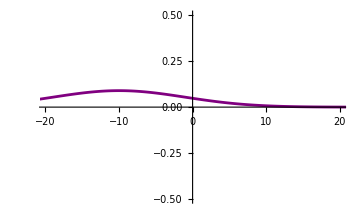

```mathematica
ListPlot[MapApply[{#1,2 #2}&]@tabU//Re, Joined->True, PlotRange->{{-20,20},{-0.5,0.5}},  PlotStyle->{{Purple},{Purple}, {Purple},{Purple}} ]
```

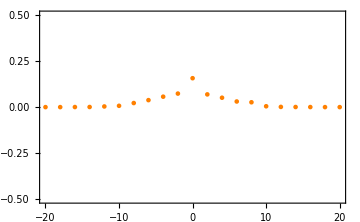

```mathematica
ListPlot[up, Joined->False, PlotRange->{{-20,20},{-0.5,0.5}},  PlotStyle->{{Orange},{Orange}, {Orange},{Orange}} ]
```